```mathematica
(* Sound testing *)
```

```mathematica
filterLevel=10000

Print["ZEROS: "]
loc="Desktop/audio_raw/0-zero1.wav"
aZero1=Import[loc]
aZeroDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel]

loc="Desktop/audio_raw/0-zero2.wav"
aZero2=Import[loc];
aZeroDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/0-zero3.wav"
aZero3=Import[loc];
aZeroDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/0-zero4.wav"
aZero4=Import[loc];
aZeroDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["ONES: "]
loc="Desktop/audio_raw/1-one1.wav"
aOne1=Import[loc];
aOneDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/1-one2.wav"
aOne2=Import[loc];
aOneDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/1-one3.wav"
aOne3=Import[loc];
aOneDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/1-one4.wav"
aOne4=Import[loc];
aOneDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["TWOS: "]
loc="Desktop/audio_raw/2-two1.wav"
aTwo1=Import[loc];
aTwoDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/2-two2.wav"
aTwo2=Import[loc];
aTwoDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/2-two3.wav"
aTwo3=Import[loc];
aTwoDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/2-two4.wav"
aTwo4=Import[loc];
aTwoDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["THREES: "]
loc="Desktop/audio_raw/3-three1.wav"
aThree1=Import[loc];
aThreeDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/3-three2.wav"
aThree2=Import[loc];
aThreeDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/3-three3.wav"
aThree3=Import[loc];
aThreeDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

loc="Desktop/audio_raw/3-three4.wav"
aThree4=Import[loc];
aThreeDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

aDat={{aZeroDat1,aZero2,aZeroDat3,aZeroDat4},{aOneDat1,aOneDat2,aOneDat3,aOneDat4},{aTwoDat1,aTwoDat2,aTwoDat3,aTwoDat4},{aThreeDat1,aThreeDat2,aThreeDat3,aThreeDat4}};
```

10000

ZEROS:

Desktop/audio_raw/0-zero1.wav

-Graphics-

SampledSoundList[{{-0.000491879,-0.000418464,-0.000555691,-0.000630011,-0.000491213,-0.00062828,-0.00070707,-0.000697935,-0.000662084,-0.000537628,-0.000597015,«88178»,0.00174137,0.00185249,0.00181379,0.00168674,0.00174489,0.00162073,0.00174034,0.00173647,0.00176234,0.00169545,0.00178128},{«1»}},44100]

Desktop/audio_raw/0-zero2.wav

Desktop/audio_raw/0-zero3.wav

Desktop/audio_raw/0-zero4.wav

ONES:

Desktop/audio_raw/1-one1.wav

Desktop/audio_raw/1-one2.wav

Desktop/audio_raw/1-one3.wav

Desktop/audio_raw/1-one4.wav

TWOS:

Desktop/audio_raw/2-two1.wav

Desktop/audio_raw/2-two2.wav

Desktop/audio_raw/2-two3.wav

Desktop/audio_raw/2-two4.wav

THREES:

Desktop/audio_raw/3-three1.wav

Desktop/audio_raw/3-three2.wav

Desktop/audio_raw/3-three3.wav

Desktop/audio_raw/3-three4.wav

```mathematica
(*test=Abs[FourierDCT[aDat[[1,1,1,1]]]]*)

aDatFTs=Table[Abs[FourierDCT[aDat[[i,j,1,1]]]],{i,1,aDat//Length},{j,1,aDat[[i]]//Length}]

aDatFTs[[1,2]]=aDatFTs[[1,2,1]]; (*Special case...*)

aDatFTs=Table[aDatFTs[[i,j]][[;;10000]],{i,1,4},{j,1,4}] (*remove 10,000->90,000 b/c they offer little data*)
(*aDatFTs=Table[aDat[[i,j,1,1]],{i,1,4},{j,1,4}]*)
```

{«1»}

{«1»}

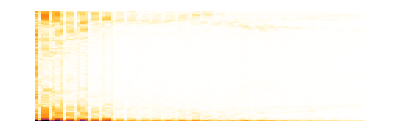
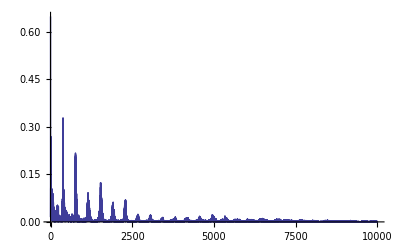
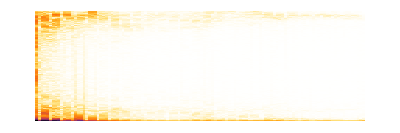
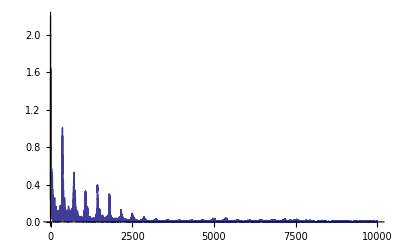
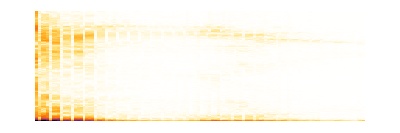
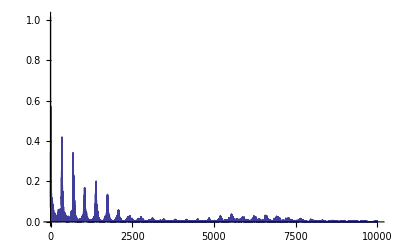
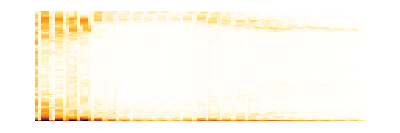
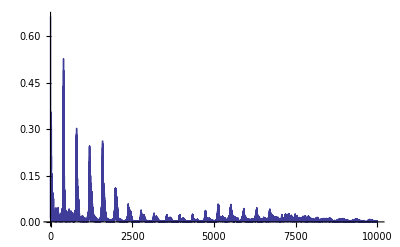

```mathematica
(*FourierAndSpec[dat_]:=Module[{},
Table[ListLinePlot[aDatFTs[[i,j]],PlotRange->All],{i,1,4},{j,1,4}]
]*)

FourierAndSpec[dat_]:=Module[{},
{Spectrogram[dat],ListLinePlot[dat,PlotRange->All]}
]

res=Table[FourierAndSpec[aDatFTs[[i,j]]],{i,1,aDat//Length},{j,1,aDat[[i]]//Length}] (*visual of FTs across all samples*)
```

{{1.13191,0.115846,0.491766,0.108985,0.170351,0.482514,0.311329,0.195609,0.1504,0.219041,0.319952,0.343443,0.160789,«9975»,0.00243505,0.00140364,0.00253475,0.00209379,0.00182226,0.00246747,0.0023603,0.0021592,0.00190079,0.00308584,0.000333313,0.00328829},«2»,{«1»}}

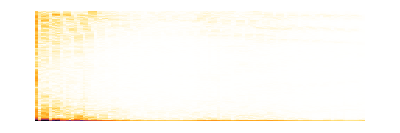
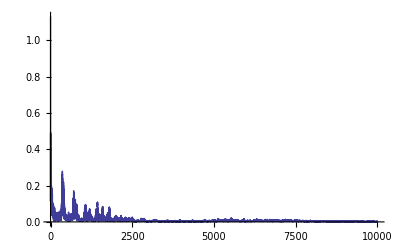
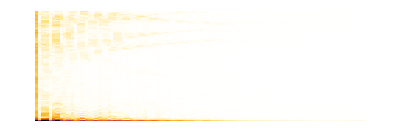
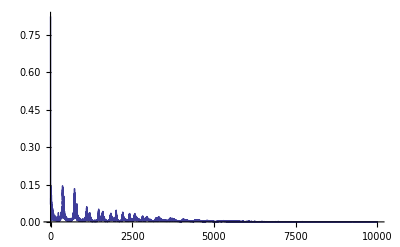
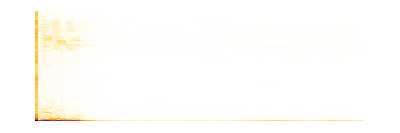
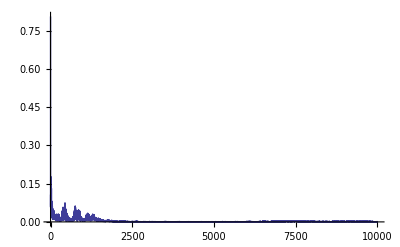
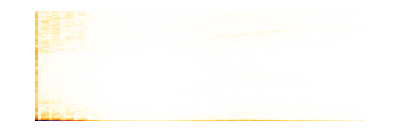
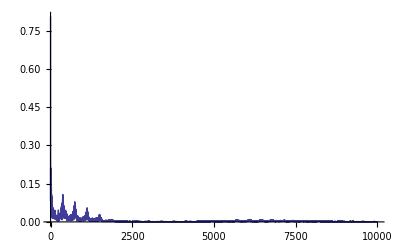

```mathematica
avgFT[FTset_]:=Module[{numSamples=0,numDataPoints=0,allAtPos=0,localAvgFT=0},
numSamples=FTset//Length;
numDataPoints=FTset[[1]]//Length;
(*Print["numSamples: ", numSamples,", numDataPoints: ",numDataPoints];*)
allAtPos=Table[FTset[[j,k]],{k,1,numDataPoints},{j,1,numSamples}];
localAvgFT=Table[Total[allAtPos[[i]]]/numSamples,{i,1,numDataPoints}]
]


aDatFTavg=Table[avgFT[aDatFTs[[i]]],{i,1,aDat//Length}] (*avg FT across samples*)
res=Table[{Spectrogram[aDatFTavg[[i]]],ListLinePlot[aDatFTavg[[i]],PlotRange->All]},{i,1,aDatFTavg//Length}] (*visual of FTs*)
```

{1,x,x^2,x^3,x^3,x^4,x^5,x^6}

{0.074373-0.0000680644 x+3.19497×10^-8 x^2-8.83668×10^-12 x^3+1.40503×10^-15 x^4-1.15347×10^-19 x^5+3.73773×10^-24 x^6,0.0384792-0.0000456566 x+2.92006×10^-8 x^2-9.25259×10^-12 x^3+1.47824×10^-15 x^4-1.15012×10^-19 x^5+3.47117×10^-24 x^6,0.0388515-0.0000417911 x+1.97015×10^-8 x^2-5.04971×10^-12 x^3+7.22285×10^-16 x^4-5.3462×10^-20 x^5+1.58399×10^-24 x^6,0.0515499-0.000063451 x+3.28427×10^-8 x^2-8.89005×10^-12 x^3+1.3177×10^-15 x^4-1.00296×10^-19 x^5+3.04375×10^-24 x^6}

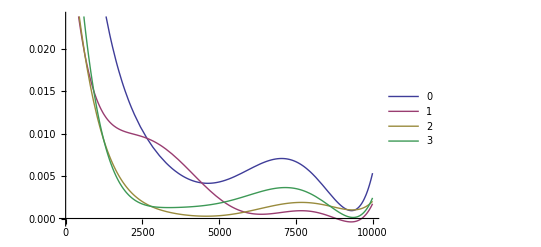

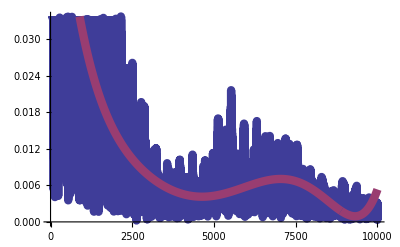
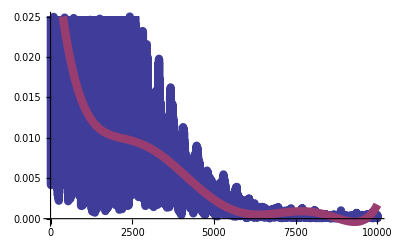
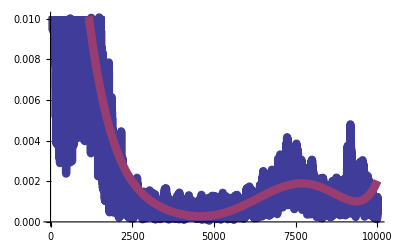
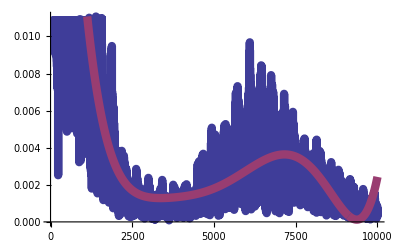

```mathematica
accuracyPoly={1,x,x^2,x^3,x^3,x^4,x^5,x^6}
fits=Table[Fit[aDatFTavg[[i]],accuracyPoly,x],{i,1,aDatFTavg//Length}]


Plot[Tooltip[{fits[[1]],fits[[2]],fits[[3]],fits[[4]]},{"1","2","3","4"}],{x,0,10000},PlotLegends->{0,1,2,3}]
Table[ListLinePlot[{aDatFTavg[[i]],Table[fits[[i]],{x,0,10000}]},PlotStyle->{Thickness[0.015]}],{i,1,fits//Length}]
```

Desktop/audio_raw/1-one1.wav

-Graphics-

0.0407766-0.0000368176 x+1.89392×10^-8 x^2-5.36074×10^-12 x^3+8.01869×10^-16 x^4-5.95733×10^-20 x^5+1.73349×10^-24 x^6

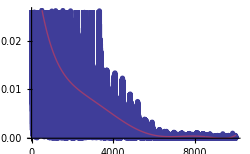

{{0,52.2142},{1,10.1672},{2,32.3602},{3,34.2821}}

```mathematica
(*READ IN SOME SOUND and check it*)

(*loc="Desktop/audio_raw/0-zero1.wav"*)
(*loc="Desktop/audio_raw/0-zero2.wav"*)
(*loc="Desktop/audio_raw/0-zero3.wav"*)
(*loc="Desktop/audio_raw/0-zero4.wav"*)
loc="Desktop/audio_raw/1-one1.wav"
(*loc="Desktop/audio_raw/1-one2.wav"*)
(*loc="Desktop/audio_raw/1-one3.wav"*)
(*loc="Desktop/audio_raw/1-one4.wav"*)
(*loc="Desktop/audio_raw/2-two1.wav"*)
(*loc="Desktop/audio_raw/2-two2.wav"*)
(*loc="Desktop/audio_raw/2-two3.wav"*)
(*loc="Desktop/audio_raw/2-two4.wav"*)
(*loc="Desktop/audio_raw/3-three1.wav"*)
(*loc="Desktop/audio_raw/3-three2.wav"*)
(*loc="Desktop/audio_raw/3-three3.wav"*)
(*loc="Desktop/audio_raw/3-three4.wav" *)
sound=Import[loc]
soundDat=HighpassFilter[Import[loc,"SampledSoundList"],10000];

someSoundFT=Abs[FourierDCT[soundDat[[1,1]]]][[;;10000]];
(*someSoundFT=aDatFTs[[1,1]] (*Pre-computed FTs for testing*) *)

accuracyPoly={1,x,x^2,x^3,x^3,x^4,x^5,x^6};
testFit=Fit[someSoundFT,accuracyPoly,x]

ListLinePlot[{someSoundFT,Table[testFit,{x,0,10000}]},PlotStyle->{Thickness[0.015],PlotRange->{{0,10000},{0,0.3}}}]

Table[{i-1,NIntegrate[Abs[fits[[i]]-testFit],{x,0,10000}]},{i,1,4}]
```